## Real gluon emission contribution to qq̄→(χ̃)_i^0(χ̃)_j^0

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Real emission contributions to neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts", "FeynHelpers"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`

FCClearScalarProducts[];
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "NLO"}];
LOResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

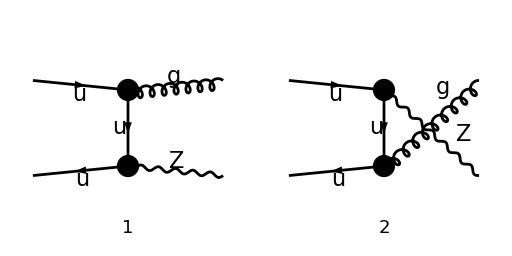

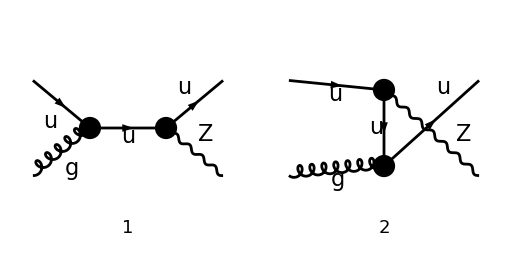

```mathematica
GluDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2], 
	{F[3, {1}], -F[3, {1}]} -> {V[5], V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}(*,
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}*)
];
Paint[GluDiagrams, Numbering->Simple, ColumnsXRows -> {2, 1}, ImageSize->{512,256}];

QrkDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2], 
	{F[3, {1}], V[5]} -> {F[3, {1}], V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}(*,
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}*)
];
Paint[QrkDiagrams, Numbering->Simple, ColumnsXRows -> {2, 1}, ImageSize->{512,256}];
```

```mathematica
Mglu[0] = FCFAConvert[
	CreateFeynAmp[GluDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {k, q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {ν,μ},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;

Mqrk[0] = FCFAConvert[
	CreateFeynAmp[QrkDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {k, q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {ν,μ},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;
```

```mathematica
{Mglu[1], Mqrk[1]} = {Mglu[0], Mqrk[0]} /. ZSimplifyRules;
{Mglu[2], Mqrk[2]} = DiracSimplify /@ Total /@ {Mglu[1], Mqrk[1]};
```

## Set scalar products

```mathematica
FCClearScalarProducts[];
SetMandelstamParameters[s, t, u, Q2];
SetMandelstam[s, t, u, ki, kj, -k, -q, 0, 0, 0, Sqrt[Q2]];
```

## Evaluate square amplitudes

### Gluon emission

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
GluTensor[0] = (Mglu[2] ConjugateAmplitude[Mglu[2]/.μ->ν]) //
	FeynAmpDenominatorExplicit //FermionSpinSum // DiracSimplify //
	DoPolarizationSums[#, k, 0]&;
GluTensor[1] = SelectFree2[GluTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = (CA CF)/2 SMP["g_s"]^2 SMP["g_W"]^2;
GluTensor[2] =  CommonPrefactor(GluTensor[1]/CommonPrefactor // SUNSimplify //
	Collect2[#, Pair[__], Factoring->Function[x, Simplify[TrickMandelstam[x, MandelstamParameters]]]]&)
```

1/2 C_A C_F g_s^2 g_W^2 (-(2 g^μν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t^2+2 (D-4) t u+(D-2) u^2+4 Q2^2-4 Q2 (t+u)))/(t u)+(4 (D-4) s k^ν q^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(4 (D-4) s k^μ q^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)-(4 (D-2) Q2 k^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)-(4 (D-2) Q2 k^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(4 k^ν k_j^μ (2 t-(D-4) s) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(4 k^μ k_j^ν (2 t-(D-4) s) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(4 q^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) (D (t+u)-2 Q2+4 s))/(t u)+(4 q^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2) (D (t+u)-2 Q2+4 s))/(t u)-(4 k_i^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t+(D-4) u-2 Q2))/(t u)-(4 k_i^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t+(D-4) u-2 Q2))/(t u)-(8 k_j^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) (D (t+u)+2 s-2 u))/(t u)-(8 q^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/t-(8 q^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/t)

```mathematica
Pair[LorentzIndex[μ,D],Momentum[q,D]].GluTensor[2] // Contract // Factor2 // TrickMandelstam[#, MandelstamParameters]&
```

(C_A C_F g_s^2 g_W^2 ((C_qqZ^L)^2+(C_qqZ^R)^2) (-D t^2-D t u+2 Q2^2-6 Q2 s+2 s^2-2 u^2) (k^ν+q^ν-k_i^ν-k_j^ν))/(t u)

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
GluTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] GluTensor[2] // DoPolarizationSums[#, q]&;
GluTensorContracted[1] = GluTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

((D-2) C_A C_F g_s^2 g_W^2 ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t^2+2 (D-4) t u+(D-2) u^2+4 Q2^2-4 Q2 (t+u)))/(t u)

### Quark emission

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
QrkTensor[0] = (Mqrk[2] ConjugateAmplitude[Mqrk[2]/.μ->ν]) //
	FeynAmpDenominatorExplicit // FermionSpinSum // DiracSimplify //
	DoPolarizationSums[#, kj, 0]&;
QrkTensor[1] = SelectFree2[QrkTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a common prefactor.

```mathematica
CommonPrefactor = (CA CF)/2 SMP["g_s"]^2 SMP["g_W"]^2;
QrkTensor[2] =  CommonPrefactor(QrkTensor[1]/CommonPrefactor // SUNSimplify //
	Collect2[#, Pair[__], Factoring->Function[x, Simplify[TrickMandelstam[x, MandelstamParameters]]]]&)
```

1/2 C_A C_F g_s^2 g_W^2 ((2 g^μν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) Q2^2-2 Q2 ((D-4) t+2 u)+(D-2) t^2+4 t u+4 u^2))/(s u)+(4 k^ν q^μ ((D-2) Q2-(D-4) t) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)+(4 k^μ q^ν ((D-2) Q2-(D-4) t) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)+(4 k^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2) (-((D-4) Q2)+(D-2) t+2 u))/(s u)+(4 k^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) (-((D-4) Q2)+(D-2) t+2 u))/(s u)+(8 k^μ k^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) (D Q2-D t+2 t-2 u))/(s u)-(4 k^ν k_j^μ (2 s-(D-4) t) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)-(4 k^μ k_j^ν (2 s-(D-4) t) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)+(4 (D-4) t q^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)+(4 (D-4) t q^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)-(4 (D-2) Q2 k_i^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)-(4 (D-2) Q2 k_i^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(s u)+(8 q^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/s+(8 q^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/s)

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
QrkTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] QrkTensor[2] // DoPolarizationSums[#, q]&;
QrkTensorContracted[1] = QrkTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

-((D-2) C_A C_F g_s^2 g_W^2 ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) Q2^2-2 Q2 ((D-4) t+2 u)+(D-2) t^2+4 t u+4 u^2))/(s u)

```mathematica
TF = 1/2;
(2CA)/(TF(Cq[L]^2+Cq[R]^2)SMP["g_s"]^2SMP["g_W"]^2)1/(4CA(CA^2-1))QrkTensorContracted[0] // SUNSimplify // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

-((D-2) ((D-2) Q2^2-2 Q2 ((D-4) t+2 u)+(D-2) t^2+4 t u+4 u^2))/(2 s u)

```mathematica
(D-2)(-4(Q2*t)/(u*s)+2(4-D)-(D-2)(u/s+s/u)) // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

-((D-2) ((D-2) Q2^2-2 Q2 ((D-4) t+2 u)+(D-2) t^2+4 t u+4 u^2))/(s u)

## Phase Space Integration

Setting up some assumptions

```mathematica
$Assumptions = {
	s ∈ PositiveReals,
	Q2 ∈ PositiveReals,
	MEW[_] ∈ PositiveReals,
	z > 0,
	z < 1,
	zInv > 0,
	zInv < 1,
	s >= (MEW[i]+MEW[j])^2,
	Q2 >= (MEW[i]+MEW[j])^2,
	Epsilon ∈ NegativeReals,
	EpsilonIR ∈ NegativeReals,
	ScaleMu ∈ PositiveReals,
	D ∈ PositiveReals
};
```

### Neutralino tensor

Importing neutralino tensor.

```mathematica
NNTensor = Import[FileNameJoin[{LOResultsDir, "NNTensor.m"}]]
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^(′′L) Conjugate[(O_ij^(′′L))]+O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(3 Q2^2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))+(g_W^2 (ḡ)^μν (Conjugate[(O_ij^(′′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′L)-6 Q2 m_i m_j O_ij^(′′R))+Conjugate[(O_ij^(′′R))] (-6 Q2 m_i m_j O_ij^(′′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′R)+m_i^2 (Q2-2 m_j^2) O_ij^(′′R)+m_i^4 O_ij^(′′R))))/(3 Q2 (Q2-Δ_Z) (Q2-Conjugate[(Δ_Z)]))))/(4 π √Q2)

### Hadronic tensors

```mathematica
PiHad = ((1-z)^(D-3)(Q2/z)^((D-4)/2))/(2^(D-1)Pi^((D-2)/2)Gamma[(D-2)/2])y^((D-4)/2)(1-y)^((D-4)/2);
```

```mathematica
MandelstamReplacements = {t -> -Q2/z(1-z)(1-y), u -> -Q2/z(1-z)y};
CommonPrefactor = 16 Pi CA CF SMP["alpha_s"]alphaW(Cq[L]^2+Cq[R]^2);
```

```mathematica
Integrand = PiHad GluTensorContracted[1] /. MandelstamReplacements // FCReplaceD[#, D->4-2EpsilonIR]&;
Result = Integrate[Integrand/CommonPrefactor, {y, 0, 1}];
% // Normal;
% /. {SMP["g_s"] -> ScaleMu^EpsilonIR Sqrt[4Pi SMP["alpha_s"]], SMP["g_W"] -> Sqrt[4Pi alphaW]};
% // Expand // ReplaceRepeated[SuperChargeRules];
GluTensorResult = CommonPrefactor Simplify[%]
```

-(16 π C_A C_F (ε_IR-1) α_s α_W μ^(2 ε_IR) -ε_IR (1-z)^(-2 ε_IR-1) (-(z^2+1) 2^(2 ε_IR+1) ε_IR π^ε_IR+(z^2+1) (4 π)^ε_IR+(z-1)^2 2^(2 ε_IR+1) ε_IR^2 π^ε_IR) ((C_qqZ^L)^2+(C_qqZ^R)^2) (z/Q2)^ε_IR)/(2-2 ε_IR)

```mathematica
Integrand = PiHad QrkTensorContracted[1] /. MandelstamReplacements // FCReplaceD[#, D->4-2EpsilonIR]&;
Result = Integrate[Integrand/CommonPrefactor, {y, 0, 1}];
% // Normal;
% /. {SMP["g_s"] -> ScaleMu^EpsilonIR Sqrt[4Pi SMP["alpha_s"]], SMP["g_W"] -> Sqrt[4Pi alphaW]};
% // Expand // ReplaceRepeated[SuperChargeRules];
QrkTensorResult = CommonPrefactor Simplify[%]
```

-(C_A C_F (ε_IR-1) (4 π)^(ε_IR+1) α_s α_W -ε_IR ((-5 z^2+6 z-7) ε_IR+(z+1)^2 ε_IR^2+4 z^2-4 z+2) ((C_qqZ^L)^2+(C_qqZ^R)^2) (z/Q2)^(ε_IR-1) (μ/(1-z))^(2 ε_IR))/(s 2-2 ε_IR)

## Total Cross-Sections

Import Born cross-section and substitute shorthands for kinetic bits.

```mathematica
MakeBoxes[K1, TraditionalForm] = SubscriptBox["K", 1];
MakeBoxes[K2, TraditionalForm] = SubscriptBox["K", 2];
KineticTermShorthands = {
	MEW[i]^4:> -12K1[Q2] - MEW[i]^2(Q2-2MEW[j]^2) - Q2 MEW[j]^2 - MEW[j]^4 + 2Q2^2,
	MEW[i] MEW[j] :> K2[Q2]/Q2};
```

```mathematica
BornXSec[0] = DiracDelta[1-z]/s(D-2)/2 (Import[FileNameJoin[{LOResultsDir, "NNxsec_hino.m"}]] // ReplaceAll[#, s->Q2]&) /.
	{Abs[a_] -> Sqrt[a*a], Re[a_ b_] -> 1/2(a b + a*b*), Re[a_] -> 1/2(a + a*)} //
	ReplaceAll[#, KineticTermShorthands]&
BornXSec[1] = BornXSec[0] // FCReplaceD[#, D -> 4-2Epsilon]&;
```

(π (D-2) p z-1 α_W^2 (1/2)^(i,j) (2 K_2(Q2) (Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)])+4 K_1(Q2) (Z_((χ̃)_i^0(χ̃)_j^0)^LR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Z_((χ̃)_i^0(χ̃)_j^0)^RL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]+Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)]+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)])))/(2 Q2^(3/2) s C_A)

### Calculate Total Cross-Sections

```mathematica
GluXSecPrefactor = 1/(4Pi s)1/(4 CA^2)IdenticalPartFactor[i,j];
QrkXSecPrefactor = 1/(4Pi s)1/(4 CA(CA^2-1))IdenticalPartFactor[i,j];
```

### Gluon emission

```mathematica
TotGluXSec[0] = GluXSecPrefactor (-Coefficient[NNTensor, Pair[LorentzIndex[μ],LorentzIndex[ν]]]) GluTensorResult //
	FeynAmpDenominatorExplicit //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, {SMP["g_W"] -> Sqrt[4Pi alphaW], SMP["g_s"]->Sqrt[4Pi SMP["alpha_s"]]}]& //
	ReplaceRepeated[#, SuperChargeRules]& //
	ReplaceAll[#, Den[s,DZ_] -> 1/(Q2-DZ)]& //
	Collect2[#, {DiracDelta[1-z], PlusDistribution}, Factoring->Function[x, Collect2[x, EpsilonIR, Factoring->Simplify]]]&;
```

```mathematica
TotGluXSec[1] = TotGluXSec[0] // ReplaceAll[#, z -> 1-zInv]& // ReplaceAll[#, KineticTermShorthands]& //
	ReplaceAll[#,  {(a_/zInv)^p_ -> a^p zInv^(-p), (a_/(1-zInv))^p_ -> a^p (1-zInv)^(-p)}]&//
	Expand //
	ReplaceAll[#, zInv^(-2EpsilonIR-1) -> -1/(2EpsilonIR)DiracDelta[zInv] + PlusDistribution[1/zInv] - 2EpsilonIR PlusDistribution[Log[zInv]/zInv]]& //
	ReplaceAll[#, zInv -> 1-z]& //
	Series[#, {EpsilonIR, 0, 0}, Assumptions->{EpsilonIR < 0}]& // Normal //
	Collect2[#, {DiracDelta, PlusDistribution}, Factoring -> Simplify]&;

TotGluXSec[2] = ((SelectNotFree2[TotGluXSec[1]//Expand, DiracDelta]/DiracDelta[1-z]/.{Q2->s, z->1})DiracDelta[1-z] + SelectFree2[TotGluXSec[1]//Expand, DiracDelta]) //
	Collect2[#, EpsilonIR, Factoring -> Function[x, Collect2[x, {DiracDelta, PlusDistribution}, Factoring -> FullSimplify]]]&
```

-(2 C_F p (z+1) (1/2)^(i,j) (log(Q2)-2 log(μ)+2 log(1-z)-log(4 π z)+ℽ+1) α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(Q2)+K_2(Q2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A Q2^(3/2) s)+(4 C_F p (1/2)^(i,j) (log(Q2)-2 log(μ)-log(4 π z)+ℽ+1) (1/(1-z))_+ α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(Q2)+K_2(Q2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A Q2^(3/2) s)+(8 C_F p (1/2)^(i,j) ((log(1-z))/(1-z))_+ α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(Q2)+K_2(Q2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A Q2^(3/2) s)+(2 C_F p z-1 (1/2)^(i,j) α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(s)+K_2(s) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A ε_IR^2 s^(5/2))+1/(2 C_A s^(5/2))C_F p z-1 (1/2)^(i,j) (2 log^2(s)+4 (-2 log(μ)-log(4 π)+ℽ+1) log(s)-8 (1+ℽ) log(2 μ)+8 log(μ) log(4 π μ)+2 log(π) (-2+log(16)+log(π))-4 ℽ (-1+log(π))+8 log^2(2)-π^2+2 ℽ^2) α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(s)+K_2(s) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2+1/ε_IR((2 C_F p (z+1) (1/2)^(i,j) α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(Q2)+K_2(Q2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A Q2^(3/2) s)-(4 C_F p (1/2)^(i,j) (1/(1-z))_+ α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(Q2)+K_2(Q2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A Q2^(3/2) s)-(2 C_F p z-1 (1/2)^(i,j) (log(s)-2 log(μ)-log(4 π)+ℽ+1) α_s (2 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) K_1(s)+K_2(s) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)) α_W^2)/(C_A s^(5/2)))

```mathematica
((4Pi ScaleMu^2)/Q2)^(-EpsilonIR)Gamma[1-2EpsilonIR]/Gamma[1-EpsilonIR] 1/(1-EpsilonIR)GluTensorResult/(16Pi CA CF alphaW SMP["alpha_s"](Cq[L]^2+Cq[R]^2))  //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, {SMP["g_W"] -> Sqrt[4Pi alphaW], SMP["g_s"]->Sqrt[4Pi SMP["alpha_s"]]}]&;
% // ReplaceAll[#, z -> 1-zInv]& // ReplaceAll[#, KineticTermShorthands]& //
	ReplaceAll[#,  {(a_/zInv)^p_ -> a^p zInv^(-p), (a_/(1-zInv))^p_ -> a^p (1-zInv)^(-p)}]&//
	Expand //
	ReplaceAll[#, zInv^(-2EpsilonIR-1) -> -1/(2EpsilonIR)DiracDelta[zInv] + PlusDistribution[1/zInv] - 2EpsilonIR PlusDistribution[Log[zInv]/zInv]]& //
	ReplaceAll[#, zInv -> 1-z]& //
	Series[#, {EpsilonIR, 0, 0}, Assumptions->{EpsilonIR < 0}]& // Normal //
	Collect2[#, {DiracDelta, PlusDistribution}, Factoring -> Simplify]&;
((SelectNotFree2[%//Expand, DiracDelta]/DiracDelta[1-z]/.{Q2->s, z->1})DiracDelta[1-z] + SelectFree2[%//Expand, DiracDelta]) //
	Collect2[
	#,
	EpsilonIR,
	Factoring -> Function[x, Collect2[
	x,
	{DiracDelta},
	Factoring -> (FullSimplify[#(*/.{a_+b_ PlusDistribution[c_] :> (a/c+b)PlusDistribution[c]}*)]&)]]]&
```

(z-1)/ε_IR^2+(z-2 (1/(1-z))_++1)/ε_IR+(z+1) (log(z)-2 log(1-z))-2 (1/(1-z))_+ log(z)+4 (-(log(1-z))/(z-1))_+

```mathematica
-2(1+z)Log[1-z] + 4PlusDistribution[Log[1-z]/(1-z)] /. a_+b_ PlusDistribution[c_] :> (a/c+b)PlusDistribution[c] // Simplify
(1+z)Log[z] - 2Log[z]PlusDistribution[1/(1-z)] /. a_+b_ PlusDistribution[c_] :> (a/c+b)PlusDistribution[c] // Simplify
```

2 (z^2+1) ((log(1-z))/(1-z))_+

-((z^2+1) (1/(1-z))_+ log(z))

```mathematica
(1-EpsilonIR)Gamma[1-EpsilonIR]/Gamma[1-2EpsilonIR] // Series[#, {EpsilonIR, 0, 1}]&
```

1+(-1-ℽ) ε_IR+O(ε_IR^2)

### Quark emission

```mathematica
TotQrkXSec[0] = QrkXSecPrefactor (-Coefficient[NNTensor, Pair[LorentzIndex[μ],LorentzIndex[ν]]]) QrkTensorResult //
	FeynAmpDenominatorExplicit //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, {SMP["g_W"] -> Sqrt[4Pi alphaW], SMP["g_s"]->Sqrt[4Pi SMP["alpha_s"]]}]& //
	ReplaceRepeated[#, SuperChargeRules]& //
	ReplaceAll[#, Den[s,DZ_] -> 1/(Q2-DZ)]& //
	Collect2[#, {DiracDelta[1-z], PlusDistribution}, Factoring->Function[x, Collect2[x, EpsilonIR, Factoring->Simplify]]]& //
	SUNSimplify
```

```mathematica
TotQrkXSec[1] = TotQrkXSec[0] // ReplaceAll[#, z -> 1-zInv]& // ReplaceAll[#, KineticTermShorthands]& //
	Expand //
	ReplaceAll[#, zInv^(-2EpsilonIR-1) -> -1/(2EpsilonIR)DiracDelta[zInv] + PlusDistribution[1/zInv] - 2EpsilonIR PlusDistribution[Log[zInv]/zInv]]& //
	ReplaceAll[#, zInv -> 1-z]& //
	Series[#, {EpsilonIR, 0, 0}]& // Normal //
	Collect2[#, {DiracDelta, PlusDistribution}, Factoring -> Simplify]&;
TotQrkXSec[2] = ((SelectNotFree2[TotQrkXSec[1]//Expand, DiracDelta]/DiracDelta[1-z]/.{Q2->s, z->1})DiracDelta[1-z] + SelectFree2[TotQrkXSec[1]//Expand, DiracDelta]) //
	Collect2[#, EpsilonIR, Factoring -> Function[x, Collect2[x, {DiracDelta, PlusDistribution}, Factoring -> FullSimplify]]]&
```

1/(2 √Q2 s^2 z (C_A^2-1))p C_F α_s α_W^2 (1/2)^(i,j) (-2 (2 (z-1) z+1) log((π z)/Q2)+(-8 (z-1) z-4) log(-(2 μ)/(z-1))+(z-2) z+ℽ (4 (z-1) z+2)+5) (2 K_1(Q2) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)+K_2(Q2) (Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]))-(p (2 (z-1) z+1) C_F α_s α_W^2 (1/2)^(i,j) (2 K_1(Q2) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)+K_2(Q2) (Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)])))/(√Q2 s^2 z (C_A^2-1) ε_IR)

### Extract Born Cross-Sections

```mathematica
Sigma0 = BornXSec[0]/DiracDelta[1-z] SMP["alpha_s"]/Pi CF ((4Pi ScaleMu^2)/Q2)^((4-D)/2)Gamma[(D-2)/2]/Gamma[D-3];
TotGluXSec[0]/Sigma0 // FCReplaceD[#, D -> 4-2EpsilonIR]& //
	ReplaceAll[#, KineticTermShorthands]& //
	FullSimplify //
	ReplaceAll[#, z -> 1-zInv]& //
	Simplify //
	Expand //
	ReplaceAll[#, zInv^(-2EpsilonIR-1) -> -1/(2EpsilonIR)DiracDelta[zInv] + PlusDistribution[1/zInv] - 2EpsilonIR PlusDistribution[Log[zInv]/zInv]]& //
	ReplaceAll[#, zInv -> 1-z]& //
	Series[#, {EpsilonIR, 0, 0}, Assumptions->{EpsilonIR<0}]& // Normal //
	ReplaceAll[#, Q2 -> z s]& //
	Collect2[#, EpsilonIR, Factoring -> Function[x, Collect2[x, {DiracDelta, PlusDistribution}, Factoring -> FullSimplify]]]&;
% /. {Log[1/z] -> -Log[z], Log[1/z-1] -> Log[1-z]-Log[z]};
(Coefficient[%, DiracDelta[1-z]]/.z->1)DiracDelta[1-z] + SelectFree2[%//Expand, DiracDelta[1-z]] /.
	PlusDistribution[1/(1-z)]Log[z] -> Log[z]/(1-z) //
	Collect2[#, EpsilonIR, Factoring -> (Collect2[#, {PlusDistribution, DiracDelta, Log}, Factoring -> Simplify]&)]&;
(*Collect2[%/.Log[1/z]->-Log[z], EpsilonIR, Factoring -> (Simplify[ReplaceRepeated[#//Expand, {Log[z]PlusDistribution[f_] -> Log[z]f, a_+b_ PlusDistribution[c_] :> (a/c+b)PlusDistribution[c]}]]&)];*)
% // Expand // ReplaceRepeated[#, Log[z]PlusDistribution[f_]->Log[z]f]& //
	Collect2[#, EpsilonIR, Factoring -> (Collect2[#, {DiracDelta, PlusDistribution}, Factoring -> Factor2]&)]&

Export[FileNameJoin[{ResultsDir, "NNGluxsec.m"}], FCReplaceD[Sigma0, D -> 4-2Epsilon] % // FullForm // ToString];
```

(z-1)/ε_IR^2+(z-2 (1/(1-z))_++1)/ε_IR-(-2 z^2 log(1-z)+z^2 log(z)+2 log(1-z)+log(z))/(1-z)+4 ((log(1-z))/(1-z))_+

```mathematica
TF = 1/2;
Sigma0 = BornXSec[0]/DiracDelta[1-z] SMP["alpha_s"]/(2Pi)TF ((4Pi ScaleMu^2)/(z s))^((4-D)/2)Gamma[(D-2)/2]/Gamma[D-3](D-2)/2;
TotQrkXSec[0]/Sigma0 // FCReplaceD[#, D -> 4-2EpsilonIR]& //
	ReplaceAll[#, KineticTermShorthands]& //
	ReplaceAll[#, z -> 1-zInv]& //
	Expand //
	ReplaceAll[#, zInv^(-2EpsilonIR-1) -> -1/(2EpsilonIR)DiracDelta[zInv] + PlusDistribution[1/zInv] - 2EpsilonIR PlusDistribution[Log[zInv]/zInv]]& //
	ReplaceAll[#, zInv -> 1-z]& //
	Series[#, {EpsilonIR, 0, 0}]& // Normal //
	ReplaceAll[#, Q2 -> z s]& //
	SUNSimplify //
	Collect2[#, EpsilonIR, Factoring -> Function[x, Collect2[x, {DiracDelta, PlusDistribution}, Factoring -> FullSimplify]]]&;
% /. {Log[1/z] -> -Log[z], Log[1/z-1] -> Log[1-z]-Log[z]};
(Coefficient[%, DiracDelta[1-z]]/.z->1)DiracDelta[1-z] + SelectFree2[%//Expand, DiracDelta[1-z]] /.
	PlusDistribution[1/(1-z)]Log[z] -> Log[z]/(1-z) //
	Collect2[#, EpsilonIR, Factoring -> (Collect2[#, {PlusDistribution, DiracDelta, Log}, Factoring -> Simplify]&)]&
	
Export[FileNameJoin[{ResultsDir, "NNQrkxsec.m"}], FCReplaceD[Sigma0, D -> 4-2Epsilon] % // FullForm // ToString];
```

(-2 z^2+2 z-1)/ε_IR+1/2 (-7 z^2+6 z+1)+(4 z^2-4 z+2) log(1-z)+(-2 z^2+2 z-1) log(z)